# Chapter 9

```mathematica
Manipulate[Range[n],{n,1,100,1}]


Manipulate[Column[Table[x,n]],{n,1,10,1}]

Manipulate[Graphics[Style[Disk[],Hue[n]]], {n,0,1}]

Manipulate[Graphics[Style[Disk[],RGBColor[n,g,c]]], {n,0,1}, {g,0,1}, {c,0,1}]



Manipulate[IntegerDigits[x],{x,1000,9999,1}]

Manipulate[Table[Hue[RGB/n],{RGB,n-1}],{n,6,50,1}]
```

```mathematica
Manipulate[Table[Graphics[Style[RegularPolygon[6],Hue[n]]],{x}],{n,0.01,1},{x,1,10}]
```

```mathematica
Manipulate[Graphics[Style[RegularPolygon[side],{color}]],{side,5,20},{color,{Red,Green,Blue}}]
```

```mathematica
Manipulate[PieChart[Range[x]],{x,1,10}]
```

```mathematica
Manipulate[BarChart[IntegerDigits[x]],{x,100,999,1}]
```

```mathematica
Manipulate[RandomColor[x],{x,1,50,1}]
```

```mathematica
Manipulate[Column[x^Range[y]],{x,1,25,1},{y,1,10,1}]
```

```mathematica
Manipulate[NumberLinePlot[{Range[x]^q}],{x,0,10},{q,0,5}]
```

```mathematica
Manipulate[Graphics3D[Style[Sphere[],Hue[x]]],{x,{Green,Red}}]
```

# Chapter 10

```mathematica
ColorNegate[EdgeDetect[CurrentImage[]]]
```

-Graphics-

```mathematica
Manipulate[Blur[CurrentImage[],x],{x,1,20}]
```

```mathematica
Table[Blur[EdgeDetect[CurrentImage[]],x],{x,1,10,1}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ImageCollage[{CurrentImage[],EdgeDetect[CurrentImage[]],Binarize[CurrentImage[]],Blur[CurrentImage[],20]}]
```

-Graphics-

```mathematica
ImageAdd[CurrentImage[],EdgeDetect[CurrentImage[]]]
```

-Graphics-

```mathematica
Manipulate[EdgeDetect[Blur[CurrentImage[]],x],{x,1,20}]
```

```mathematica
EdgeDetect[Graphics3D[Sphere[]]]
```

-Graphics-

```mathematica
Manipulate[Blur[Graphics[Style[RegularPolygon[5],Purple]],x],{x,0,20}]
```

```mathematica
ImageCollage[Table[Graphics[Style[Disk[],RandomColor[]]],9]]
```

-Graphics-

```mathematica
Table[Graphics3D[Style[Sphere[],Hue[x]]],{x,0,1,0.2}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
Table[Blur[Graphics[Disk[]],x],{x,0,30,5}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

# Chapter 11 Problems 1-15

```mathematica
ImageAdd[{CurrentImage[],Graphics[Disk[]]}]
```

-Graphics-

```mathematica
ImageAdd[{CurrentImage[],Graphics[Style[RegularPolygon[8],Red]]}]
```

-Graphics-

```mathematica
ImageAdd[ColorNegate[EdgeDetect[CurrentImage[]]],CurrentImage[]]
```

-Graphics-

```mathematica
StringJoin["Hello","Hello"]
```

HelloHello

```mathematica
StringJoin[ToUpperCase[{Alphabet[]}]]
```

ABCDEFGHIJKLMNOPQRSTUVWXYZ

```mathematica
StringReverse[StringJoin[{Alphabet[]}]]
```

zyxwvutsrqponmlkjihgfedcba

```mathematica
StringJoin[Table["AGCT",{100}]]
```

AGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCT

```mathematica
StringTake[StringJoin[Alphabet[]],6]
```

abcdef

```mathematica
Column[StringTake["This is About Strings",Range[StringLength["This is About Strings"]]]]
```

StringTake::ambgsntx: Warning: interpreting list of integers as a list of sequence specifications.

T
Th
Thi
This
This 
This i
This is
This is 
This is A
This is Ab
This is Abo
This is Abou
This is About
This is About 
This is About S
This is About St
This is About Str
This is About Stri
This is About Strin
This is About String
This is About Strings

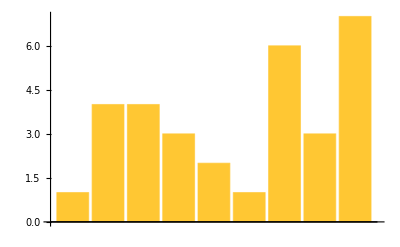

```mathematica
BarChart[StringLength[TextWords["A long time ago, in a galazy far, faraway"]]]
```

```mathematica
StringLength[{WikipediaData["Computer"]}]
```

{60266}

```mathematica
Length[TextWords[WikipediaData["computer"]]]
```

9271

```mathematica
First[TextSentences[WikipediaData["strings"]]]
```

String or strings may refer to:

```mathematica
StringJoin[StringTake[TextSentences[WikipediaData["computers"]],1]]
```

AMTTACCESEMTTTCTPP=ITTDBTTTT==DTLTTTSITIIDMTTAAATTTIASIBIAITITIITSI=CCAHTFTTTAEBNH=ITax()2{,THI=DHTTTTAB==CBTDETTITIRTZTT=PTEITDTTHACIINCTLOTIIIHBT==TTHTVTE=ECWATIHJTIIAATBAIL=TJFCJTHATHTTWITT=TTDTKIHKNNHPNIMTGFTTWISTITS=TTLTTTT=C=A=SH=TC==ATIET=WTTSC=TSC=TCATRDIRTPIWJSAIT=TES=TTSHTALTSG=AETTLSIETWOAMTTRACrRIIISFIIG=IDOHCIAMA=WTOBItSTBSIT=SMSTSS=SSCICW=T=TTMIAL=TITHTFMPWSTCBOTOI=ITTSTTITMWITC=PUTTS=MF=ATHHIT=PALTP=ETHOBSA=CTITTITCITA"=AWA=TMH=TQCVSLTTT=ACARPE=AT=====M

```mathematica
Max[StringLength[WordList[]]]
```

23

```mathematica
Count[StringTake[WordList[],1],"q"]
```

194

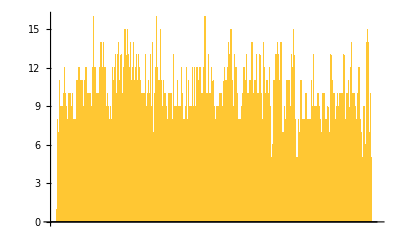

```mathematica
BarChart[Take[StringLength[WordList[]],1000]]
```

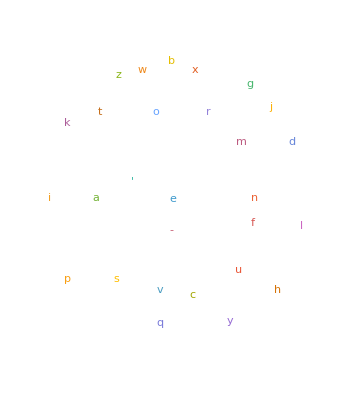

```mathematica
WordCloud[Characters[StringJoin[WordList[]]]]
```